# MatrixExp

## Basic Examples

Exponential of a 2x2 matrix:

```mathematica
MatrixExp[{{1.2,5.6},{3,4}}]
```

{{346.557,661.735},{354.501,677.425}}

```mathematica
MatrixExp[{{0,1},{-1,0}}t]
```

{{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}

Exponential applied to a vector:

```mathematica
MatrixExp[{{1.2,5.6},{3,4}},{1,2}]
```

{1670.03,1709.35}

## Applications

A system of first-order linear differential equations:

```mathematica
system = {{x'[t] == z[t]}, {y'[t] == y[t] - z[t]}, {z'[t] == -x[t]}};
```

Write the system in the v’(t)=a.v(t) with v(t)={x(t),y(t),
z(t)}:

```mathematica
a=({{0, 0, 1}, {0, 1, -1}, {-1, 0, 0}});
```

The matrix exponential gives the basic for the general solution:

```mathematica
MatrixExp[a t]//MatrixForm
```

(Cos[t] | 0 | Sin[t]
ⅇ^t/2-Cos[t]/2-Sin[t]/2 | ⅇ^t | -ⅇ^t/2+Cos[t]/2-Sin[t]/2
-Sin[t] | 0 | Cos[t])

```mathematica
DSolve[system,{x[t],y[t],z[t]},t]
```

{{x[t]→C[1] Cos[t]+C[3] Sin[t],y[t]→ⅇ^t C[2]+1/2 C[1] (ⅇ^t-Cos[t]-Sin[t])+1/2 C[3] (-ⅇ^t+Cos[t]-Sin[t]),z[t]→C[3] Cos[t]-C[1] Sin[t]}}

The matrix exponential applied to a vector gives a particular solution:

```mathematica
MatrixExp[a t, {1,0,0}]//MatrixForm
```

(Cos[t]
ⅇ^t/2-Cos[t]/2-Sin[t]/2
-Sin[t])

```mathematica
DSolve[{system,{x[0]==1,y[0]==0,z[0]==0}},{x[t],y[t],z[t]},t]
```

{{x[t]→Cos[t],y[t]→1/2 (ⅇ^t-Cos[t]-Sin[t]),z[t]→-Sin[t]}}

The matrix s approximates the second derivative periodic on [-L,L] on the grid x:

```mathematica
L=10;
n=500;
x=L*(2N[Range[n]]/n-1);
s=N[Block[{h=2.L/n},1/h^2 SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1,{1,n}->1,{n,1}->1},{n,n}]]]
```

SparseArray[…]

A vector representing a soliton on the grid x:

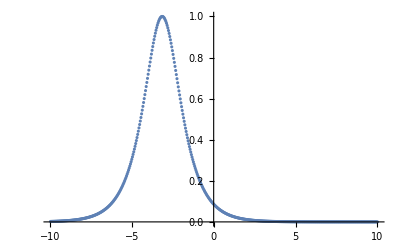

```mathematica
u=Sech[x+Pi]Exp[Pi I x];
ListPlot[Transpose[{x,Abs[u]}]]
```

Propagate the solution of ⅈ (∂u)/(∂t)=2|u|^2 u+(∂^2 u)/(∂x^2) using a splitting
ⅇ^(A+B)=ⅇ^(A/2)ⅇ^B ⅇ^(A/2)+O(Δt^2):

```mathematica
Timing[Module[{Δt=0.05,m},
m=Δt(0.+1.I)s;
Do[
u=Exp[Δt I u
Conjugate[u]]u;
u=MatrixExp[m,u];
u=Exp[Δt I u Conjugate[u]]u,{1/Δt}]]]
```

{0.21875,Null}

Plot the solution and 10 times the error from the solution of the cubic Schrödinger equation:

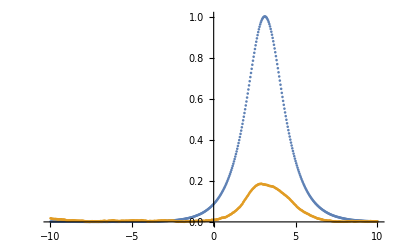

```mathematica
ListPlot[{Transpose[{x,Abs[u]}],Transpose[{x,10Abs[u-Sech[x-Pi]Exp[I(Pi x+(1-Pi^2))]]}]},PlotRange->All]
```

## Properties & Relations